## Parameters

```mathematica
(*These parameters are caught from CI*)
mg=0.8;αir=0.93π;
mu=0.007;
(*This parameter )need to be adjusted*)
Λuv=0.6;(*0.62*)
Λir=0;(*0.23*)
(*Temperature0 from 0.01 to 0.30, 0.01 every step*)
t0start=0.01;t0end=0.30;t0step=0.01;
Tinit=Table[x,{x,t0start,t0end,t0step}];
(*Minit*)
Minit=Table[0,{Length[Tinit]}];
(*-----------------------------*)

(*Temperature*)
T=0.0005;
(*μ from 0.01 to 0.5, 0.01 every step*)
μstart=0.01;μend=0.5;μstep=0.01;
μ=Table[x,{x,μstart,μend,μstep}];(*M*)
M=Table[0,{Length[μ]}];
(*Error range*)
ϵ=0.000001;
```

## Function

```mathematica
(*This function is similar to CI function C, also named Ϛ,but in different form*)


Mass[M_,T_,μ_]:=mu+M*(16*αir)/(3π*mg^2)*Ϛ[M,T,μ];
Ϛ[M_,T_,μ_]:=T*NIntegrate[SM[S,M,T,μ],{S,Λir^2,Λuv^2}];
SM[S_,M_,T_,μ_]:=∑_(n=-∞)^∞ (√S)/(S+M^2+((2n+1)π*T+I*μ)^2);

(*Calculation function, every set of (T,μ) give a number M*)

Cal[Tin_,μin_]:=Module[
							{
							T=Tin,μ=μin,
							M0,M1
							},(*Local variable*)
							M0=0;(*Initial value*)
							M1=0.37;(*Initial value*)
								(*Calculation, DS equation*)
							While[
								Abs[M1-M0]>ϵ,
								M0=M1;
								M1=Mass[M0,T,μ];	
								];
						M1	
						]
```

## Calculate

```mathematica
(*
I want to calculate two circumstances;
	1.μ=0,T≠0 ;I use it to set a reasonable parameter Λuv,in contact with Heat-Kernel regularization,put the result in Minit;
	2.μ≠0,T≠0 ;I consider them to reference results;
*)
(*----------------------*)
(*Parallelize calculation*)
CloseKernels[];
LaunchKernels[16];
SetSharedVariable[Minit,Tinit];

ParallelDo[
	Minit[[i]]=Cal[Tinit[[i]],0]
	,
	{i,Length[Tinit]}
	];
(*
Do[
Print[Minit[[i]]],
{i,Length[Minit]}
]
*)
(*----------------------*)
CloseKernels[];
LaunchKernels[16];
SetSharedVariable[M,μ];
(*Calculate different μ*)
ParallelDo[
M[[i]]=Cal[T,μ[[i]]];	
,
{i,Length[μ]}
];
```

## Draw Chart

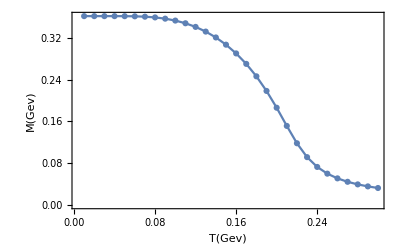

-Graphics-

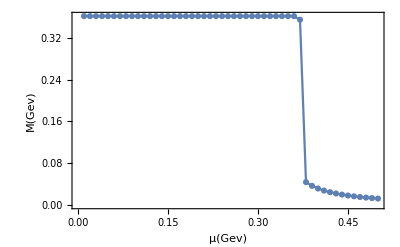

```mathematica
(*Draw chart*)
Chart0=ListLinePlot[
Transpose[{Tinit,Minit}],
PlotMarkers->Automatic,
Frame->True,
FrameLabel->{Style["T(Gev)",Bold,12.5],  Style["M(Gev)",Bold,12.5]},
PlotRange->Full

]

Chart1=ListLinePlot[
{Transpose[{μ,Abs[M]}],
Transpose[{μr,Abs[Mr]}]
},
PlotMarkers->Automatic,
Frame->True,
FrameLabel->{Style["μ(Gev)",Bold,12.5],  Style["M(Gev)",Bold,12.5]},
PlotRange->Full
]
```

## Export Result

```mathematica
(*Export["E:\\NJU\\program\\Infinite_temprature\\Result_pdf\\ZZZ_Infinite_miu_quark_mass_hard_cutoff_0.pdf", Chart0];
Export["E:\\NJU\\program\\Infinite_temprature\\Result_pdf\\ZZZ_Infinite_miu_quark_mass_hard_cutoff_1.pdf", Chart1];*)
```